```mathematica
DSolve[{y''[x]+y[x]*x^2m^4==0},y[x],x]
```

{{y[x]→C[1] ParabolicCylinderD[-1/2,(-1)^(1/4) √2 m x]+C[2] ParabolicCylinderD[-1/2,(-1)^(3/4) √2 m x]}}

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
ParabolicCylinderD[-1/2,0]
```

```mathematica
D[ParabolicCylinderD[-1/2,x],x]
```

1/2 x ParabolicCylinderD[-1/2,x]-ParabolicCylinderD[1/2,x]

```mathematica
Sol[x_,m_]:=ParabolicCylinderD[-1/2,m(1+I)x]-ParabolicCylinder[-1/2,m(-1+I)x]
```

```mathematica
FullSimplify[D[Sol[x],x]/.{x->1}]
```

ⅈ m (m ParabolicCylinderD[-1/2,(1+ⅈ) m]-(1-ⅈ) (ParabolicCylinderD[1/2,(1+ⅈ) m]+ⅈ ParabolicCylinder^(0,1)[-1/2,(-1+ⅈ) m]))

```mathematica
der[m_]:=ⅈ m (m ParabolicCylinderD[-1/2,(1+ⅈ) m]-(1-ⅈ) (ParabolicCylinderD[1/2,(1+ⅈ) m]+ⅈ Derivative[0,1][ParabolicCylinder][-1/2,(-1+ⅈ) m]))
```

```mathematica
NSolve[der[m]==0,m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→0.}}

```mathematica
FindRoot[der[m]==0,{m,0.1}]
```

FindRoot::nlnum: The function value {(0.`  + 0.1` ⅈ) ((0.11581335375890106`  - 0.0058136541018157` ⅈ) - (1.`  - 1.` ⅈ) ((0.6423699994229543`  + 0.054797137183475245` ⅈ) + (0.`  + 1.` ⅈ) SuperscriptBox[ is not a list of numbers with dimensions {1} at {m} = {0.1`}.

FindRoot[der[m]==0,{m,0.1}]

```mathematica
N[FullSimplify[der[0.1]]]
```

(-0.0581759-0.0581354 ⅈ)+(0.1-0.1 ⅈ) ParabolicCylinder^(0,1)[-0.5,-0.1+0.1 ⅈ]

```mathematica
N[Derivative[0,1][ParabolicCylinder][-0.5,0.1]]
```

ParabolicCylinder^(0,1)[-0.5,0.1]

```mathematica
N[BesselJ[-1/4,1]]
```

0.669385

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

```mathematica
fun1[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]+BesselJ[1/4,x^2/4])
```

```mathematica
fun2[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]-BesselJ[1/4,x^2/4])
```

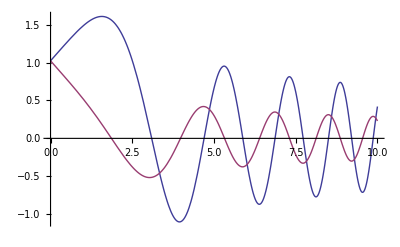

```mathematica
Plot[{fun1[x],fun2[x]},{x,0,10}]
```

```mathematica
funm1[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]+BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funm2[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]-BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funderm1=FullSimplify[D[funm1[x],x]]
```

1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]-BesselJ[3/4,(m^2 x^2)/2])

```mathematica
funderm2=FullSimplify[D[funm2[x],x]]
```

-1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]+BesselJ[3/4,(m^2 x^2)/2])

```mathematica
NSolve[funm1[0]*funderm2[1]-funm2[0]*funderm1[1]==0,m]
```

∞::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

{{}}

```mathematica
Limit[funm1[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[funm2[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
FullSimplify[funderm1/.{x->1}]
```

1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[funderm2/.{x->1}]
```

-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])==0]
```

m^(5/2) BesselJ[-3/4,m^2/2]==0

```mathematica
BesselJZero[-3/4,10]
```

```mathematica
N[BesselJZero[-3/4,1]]
```

1.05851

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,100}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729,15.92737088,16.12341118,16.31709625,16.508509,16.69772758,16.88482577,17.06987328,17.25293611,17.43407678,17.61335459,17.79082587,17.96654416,18.14056039,18.31292309,18.48367852,18.65287083,18.82054216,18.98673282,19.15148136,19.31482468,19.47679813,19.63743561,19.79676966,19.95483148,20.11165108,20.26725729,20.42167785,20.57493946,20.72706782,20.87808772,21.02802303,21.17689679,21.32473123,21.47154783,21.61736732,21.76220974,21.90609448,22.04904029,22.1910653,22.3321871,22.47242269,22.61178856,22.7503007,22.88797461,23.02482533,23.16086744,23.29611511,23.4305821,23.56428178,23.69722713,23.82943078,23.96090501,24.09166175,24.22171263,24.35106896,24.47974174,24.60774171,24.7350793,24.86176469,24.98780781}

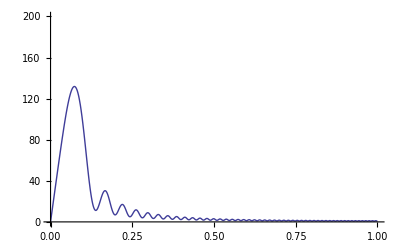

```mathematica
Plot[Sum[(funm1[x]/.{m->Zeros[[i]]})-(funm2[x]/.{m->Zeros[[i]]}),{i,1,100}],{x,0,1},PlotRange->{{0,1},{0,200}}]
```

## Testing solution

```mathematica
test=Sqrt[π x]*BesselJ[-1/4,x^2/4]
```

√π √x BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]]
```

-1/4 √π x^(5/2) BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]+x^2/4*test]
```

0

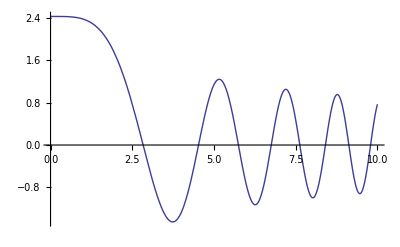

```mathematica
Plot[test,{x,0,10}]
```

```mathematica
sol1=Sqrt[m x]*BesselJ[-1/4,m^2 x^2/2]
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
sol2=Sqrt[m x]*BesselJ[1/4,m^2 x^2/2]
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Limit[sol1,x->0]
```

(√2 (m^2)^(3/4))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[sol2,x->0]
```

0

```mathematica
sol1
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
dersol1=FullSimplify[D[sol1,x]]
```

-m (m x)^(3/2) BesselJ[3/4,(m^2 x^2)/2]

```mathematica
dersol2=FullSimplify[D[sol2,x]]
```

m (m x)^(3/2) BesselJ[-3/4,(m^2 x^2)/2]

```mathematica
Limit[dersol1,x->1]
```

-m^(5/2) BesselJ[3/4,m^2/2]

```mathematica
Limit[dersol2,x->1]
```

m^(5/2) BesselJ[-3/4,m^2/2]

```mathematica
Zerostrue=Table[Sqrt[2BesselJZero[-3/4,i]],{i,1,200}];
```

```mathematica
coeffs=Table[BesselJZero[-3/4,i],{i,1,200}];
```

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,200}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729,15.92737088,16.12341118,16.31709625,16.508509,16.69772758,16.88482577,17.06987328,17.25293611,17.43407678,17.61335459,17.79082587,17.96654416,18.14056039,18.31292309,18.48367852,18.65287083,18.82054216,18.98673282,19.15148136,19.31482468,19.47679813,19.63743561,19.79676966,19.95483148,20.11165108,20.26725729,20.42167785,20.57493946,20.72706782,20.87808772,21.02802303,21.17689679,21.32473123,21.47154783,21.61736732,21.76220974,21.90609448,22.04904029,22.1910653,22.3321871,22.47242269,22.61178856,22.7503007,22.88797461,23.02482533,23.16086744,23.29611511,23.4305821,23.56428178,23.69722713,23.82943078,23.96090501,24.09166175,24.22171263,24.35106896,24.47974174,24.60774171,24.7350793,24.86176469,24.98780781,25.11321832,25.23800565,25.36217901,25.48574737,25.60871948,25.7311039,25.85290896,25.97414283,26.09481347,26.21492864,26.33449595,26.45352284,26.57201655,26.6899842,26.80743273,26.92436894,27.04079946,27.1567308,27.27216934,27.38712129,27.50159277,27.61558975,27.72911807,27.84218348,27.95479159,28.0669479,28.17865781,28.28992661,28.40075948,28.5111615,28.62113767,28.73069287,28.83983189,28.94855946,29.05688017,29.16479858,29.27231912,29.37944617,29.48618402,29.59253687,29.69850887,29.80410407,29.90932646,30.01417998,30.11866846,30.2227957,30.32656541,30.42998126,30.53304684,30.63576569,30.73814128,30.84017702,30.94187629,31.04324239,31.14427857,31.24498803,31.34537392,31.44543935,31.54518735,31.64462094,31.74374306,31.84255663,31.9410645,32.03926951,32.13717442,32.23478197,32.33209485,32.42911572,32.52584719,32.62229183,32.71845218,32.81433073,32.90992996,33.00525229,33.10030011,33.19507578,33.28958162,33.38381993,33.47779296,33.57150294,33.66495208,33.75814252,33.85107642,33.94375588,34.03618297,34.12835976,34.22028825,34.31197045,34.40340832,34.49460381,34.58555884,34.6762753,34.76675505,34.85699993,34.94701178,35.03679238,35.12634351,35.21566691,35.30476432,35.39363745}

```mathematica
Table[N[BesselJZero[-3/4,i],10],{i,1,10}]
```

{1.058508259,4.284053813,7.440454404,10.58817915,13.73311845,16.87681751,20.01985758,23.16250593,26.30490257,29.4471279}

```mathematica
N[BesselJ[3/4,BesselJZero[-3/4,3]]]
```

0.207121

```mathematica
N[BesselJ[1/4,BesselJZero[-3/4,1]]]
```

0.742897

```mathematica
sol2
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
sol2m=√x BesselJ[1/4,(m^2 x^2)/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Plot[Sum[(sol2m/.{m->Zerostrue[[i]]}),{i,1,10}],{x,0,1},PlotRange->{{0,1},{0,100}}]
```

$Aborted

```mathematica
NIntegrate[x BesselJ[1/4,x^2/2*Zerostrue[[1]]^2]*BesselJ[1/4,x^2/2*Zerostrue[[3]]^2],{x,0,1}]
```

0.0297444

```mathematica
NIntegrate[x*BesselJ[1/4,x^2*coeffs[[1]]]*BesselJ[1/4,x^2*coeffs[[2]]],{x,0,1}]
```

0.0714686

```mathematica
N[Integrate[x*BesselJ[1/4,x^2/4]BesselJ[3/4,x^2/4],{x,0,1}]]
```

0.0371135

```mathematica
Integrate[x*BesselJ[1/4,x^2/4],{x,0,1}]
```

(4 2^(1/4) HypergeometricPFQ[{5/8},{5/4,13/8},-1/64])/(5 Gamma[1/4])